ElectroDynamics, by James Rohlf and Kevin Reiss, Version 2.0, Copyright 2022, All Rights Reserved.

__________________________________________________________________________________

Section | Electric Fields in Matter

3.1 Polarization Vector
	3.2 Electric Potential from the Polarization
	3.3 Polarized Cube
	3.4 Uniformly Polarized Ball
	3.5 Displacement Vector D
	3.6 Capacitance
	3.7 Point Charge Near Dielectric  Boundary
	3.8 Stored Energy in Dielectrics

A dielectric ball placed in a uniform external electric field is an important example that will appear again in the discussion of magnetic fields in matter. The result is a uniform electric field inside the ball, which contributes to the external field as a pure dipole. It is described in Section 3.4.

```mathematica
(Column[{#[EntityProperty["WolframDemonstration","WolframDemonstrationsLink"]]/.Hyperlink[link_]:>Hyperlink[#[EntityProperty["WolframDemonstration","Name"]],link],Row[{"By: "}~Join~Riffle[(Hyperlink[#["Name"],First[#["ContributorLink"]]])&/@#[EntityProperty["WolframDemonstration","Authors"]],", "]],#[EntityProperty["WolframDemonstration","Manipulate"]],
}]&)[Entity["WolframDemonstration","DielectricSphereInAUniformElectricField"]]
```

[Dielectric Sphere in a Uniform Electric Field ](https://demonstrations.wolfram.com/DielectricSphereInAUniformElectricField)
By: [Y. Shibuya](http://demonstrations.wolfram.com/author.html?author=Y.+Shibuya)

When molecules are placed in an external electric field they get stretched. The electrons get pushed opposite the field direction. The torque on a dipole in an external field is in the direction to align the molecular dipole with the external field. The dipole moment of the distorted molecule (p) is therefore in the same direction as the external field that stretches it.

p=α E_ext

```mathematica
Graphics3D[{Thickness[0.004],Arrow[{{0,0,-.4},{0,0,.4}}],Arrow[{{1,0,-.4},{1,0,.4}}],Style[Text["+",{0,0,.6}],18,Darker[Red]],Style[Text["-",{0,0,-.6}],18],Style[Text["p",{-.2,0,0}],24,Bold],Style[Text[Subscript["E", ext],{1.4,0,0}],24,Bold],Opacity[0.3],Green,Opacity[0.2],Ellipsoid[{0,0,0},{.5,.5,.75}]},Boxed->False]
```

-Graphics3D-

The order of magnitude of α is given by

α/(4 π ε_0)∼10^-30("m")^3

Estimate the amount of atomic stretching in an external field of 5 x 10^5 "V""/""m".

```mathematica
NumberForm[UnitConvert[4π Quantity[, "ElectricConstant"](10^-30 Quantity[, "Meters"]^3)  (5 10^5 Quantity[, ("Volts")/("Meters")]), Quantity[, "ElementaryCharge"]*Quantity[, "Meters"]],1]
```

3.×10^-16 m e

Even though the amount of stretching is tiny, the collective effect of a large number of molecules can be huge.

3.1 Polarization Vector

The effect of the aligned dipoles is referred to by a polarization vector P which is defined to be the dipole moment per volume. The units of P are  "C"/ ("m")^2, the same as surface charge density. It is important to note that the polarization might be caused by an external field or it might be permanent. If it is caused by an external field (E_ext), then we write

P= ("ε")_0 χ_e E_ext

The dimensionless constant  χ_e is called the electric susceptibility.  Materials that satisfy this equation are called linear dielectrics. It applies to most materials if the fields are not too strong. For air, the breakdown is 3  "MV"/ "m" and for mica it is 200  "MV"/ "m".

3.1 Bound Surface Charge:  Line of Dipoles

Consider a linear collection of such dipoles, all lined up in an external field. Qualitatively, there is extra an charge on each end with the other charge along the line cancelling in pairs. The result looks like a longer dipole.

Draw a line of dipoles.

```mathematica
imax=10; jmax=6;kmax=3; j=0; i=0; Graphics3D[{Table[Style[Text["+",{i,j,.6+1.5 k}],18,Darker[Red]],{k,0,kmax}],Table[Style[Text["-",{i,j,-.6+1.5 k}],18],{k,0,kmax}],{Green,Opacity[0.2],Table[Ellipsoid[{i,j,1.5 k},{.5,.5,.75}],{k,0,kmax}]},Thickness[0.004],Arrow[{{1.5,0,1.5},{1.5,0,3.5}}],Style[Text[Subscript["E", ext],{2,0,2.5}],24,Bold]},Boxed->False]
```

-Graphics3D-

3.2 Bound Surface Charge:  Sheet of Dipoles

If we made a plane of dipoles, we get a line of charge on each end.

Draw a plane of dipoles.

```mathematica
imax=10; jmax=6;kmax=6; j=0; Graphics3D[{Table[Table[Style[Text["+",{i,j,.6+1.5 k}],18,Darker[Red]],{i,0,imax}],{k,0,kmax}],Table[Table[Style[Text["-",{i,j,-.6+1.5 k}],18],{i,0,imax}],{k,0,kmax}],{Green,Opacity[0.2],Table[Table[Ellipsoid[{i,j,1.5 k},{.5,.5,.75}],{i,0,imax}],{k,0,kmax}]},Thickness[0.004],Arrow[{{11.5,0,3},{11.5,0,7}}],Style[Text[Subscript["E", ext],{13,0,5}],24,Bold]},Boxed->False]
```

-Graphics3D-

3.3 Bound Surface Charge:  Cuboid of Dipoles

Finally, if we combine planes to make a cuboid, we get an accumulation of charge on the surfaces that are perpendicular to the field. This charge is bound to the atomic dipoles and is referred to as σ_b.

Draw a volume array of dipoles.

```mathematica
imax=10; jmax=6; kmax=3; Graphics3D[{Table[Table[Table[Style[Text["+",{i,j,.6+1.5 k}],18, Darker[Red]],{i,0,imax}],{j,0,jmax}],{k,0,kmax}],Table[Table[Table[Style[Text["-",{i,j,-.6+1.5 k}],18],{i,0,imax}],{j,0,jmax}],{k,0,kmax}],{Green,Opacity[0.2],Table[Table[Table[Ellipsoid[{i,j,1.5 k},{.5,.5,.75}],{i,0,imax}],{j,0,jmax}],{k,0,kmax}]},Thickness[0.004],Arrow[{{0,8,1},{0,8,4}}],Style[Text[Subscript["E", ext],{0,9,2.5}],24,Bold]},Boxed->False]
```

-Graphics3D-

3.2 Electric Potential from the Polarization

Starting with the electric potential for an ideal dipole,

V=(p \[Application] r̂)/(4 π  ("ε")_0 r^2)

one may divide a chunk of matter into differential pieces

ⅆp = P ⅆ𝕍 '

and then integrate to get the total contribution to V.

V=1/(4 π  ("ε")_0)∫  ⅆ𝕍'(P \[Application] ℛ̂)/ℛ^2

In this expression, P is not necessarily uniform; it may vary with position.

```mathematica
ClearAll["Global`*"];Graphics3D[{Thickness[0.005],Arrow[{{0,0,0},{-.5,1,0}}],Arrow[{{-.5,1,0},{2.,2.05,0}}],Arrow[{{0,0,0},{2.02,2.02,0}}],Style[Text["r'",{-.5,.4,0}],24,Bold],Style[Text["r",{1.1,.8,0}],24,Bold],Style[Text[ℛ,{.6,1.7,0}],24,Bold],{Darker[Green],Opacity[0.3],Ellipsoid[{-.5,1.1,0},{.4,.3,1} ]},Style[Text["𝒫",{2.1,2.1,0}],12],Style[Text["𝒪",{0,-.1,0}],12],Opacity[1],Darker[Gray],Sphere[{-.5,1,0},.05],Black,Arrow[{{-.5,1,0},{-.3,1.1,-.2}}],Style[Text["Pⅆ𝕍'",{-.6,1.2,0}],14,Bold]},Boxed->False]
```

-Graphics3D-

A trick can be used to get the integral in a form to integrate by parts.

∇' 1/ℛ=  (ℛ̂)/ℛ^2

```mathematica
Subscript[(∇' 1/ℛ), k]=∂_k [(Subscript[r, n]-Subscript[r', n])(Subscript[r, n]-Subscript[r', n])]^(-1/2)=(-1/2)1/ℛ^3(-Subscript[ℛ, n])(-Subscript[δ, kn])=Subscript[ℛ, k]/ℛ^3=Subscript[((ℛ̂)/ℛ^2), k]
```

Verify the vector identity.

```mathematica
r={x,y,z}; r′={x′,y′,z′};ℛ=r-r′   ;  Grad[1/(√(ℛ.ℛ)),{x′,y′,z′}]==ℛ/(ℛ.ℛ)^(3/2)
```

True

V=1/(4 π ε_0)∫ P \[Application] (∇' 1/ℛ)ⅆ𝕍'= 1/(4 π ε_0)∫ ∇' \[Application] (P/ℛ)ⅆ𝕍'-1/(4 π ε_0)∫ 1/ℛ∇'\[Application]Pⅆ𝕍'

Now we may make use of the divergence theorem on the first term on the right.

V= 1/(4 π ε_0)∫ (P \[Application]  n̂)/ℛ ⅆ𝕒'-1/(4 π ε_0)∫ (∇ '\[Application] P)/ℛ ⅆ𝕍'

From this we can interpret the bound surface charge density (σ_b) as

σ_b= P \[Application] n̂

and the bound volume charge density (ρ_b) as

ρ_b= -∇\[Application] P

The usefulness of this formulation is that we can use the bound charge distributions to get the fields instead of integrating over all the dipoles.This is an enormous simplification.

3.3 Polarized Cube

Consider a permanently polarized cube of dimension a and

P=k r

with k a constant.

```mathematica
Graphics3D[{Style[Text["P",{0,0,.2}],18,Bold],Arrow[{{0,0,0},{1,1,1}}],Arrow[{{0,0,0},{-1,1,1}}],Arrow[{{0,0,0},{-1,-1,1}}],Arrow[{{0,0,0},{-1,-1,-1}}],Arrow[{{0,0,0},{1,-1,1}}],Arrow[{{0,0,0},{1,-1,-1}}],Arrow[{{0,0,0},{-1,1,-1}}],Arrow[{{0,0,0},{1,1,-1}}],Darker[Green], Opacity[0.3],Cuboid[{-1,-1,-1},{1,1,1}]}]
```

-Graphics3D-

There is a bound volume charge density

ρ_b= -∇\[Application] P=-3k

and bound volume charge

Q_b= ρ_b a^3=-3k a^3

There is also a bound surface charge.

Calculate the bound charge on one face of the cube.

```mathematica
P=k{x,y,a/2};  n={0,0,1};∫_(-a/2)^(a/2) ∫_(-a/2)^(a/2) P.nⅆxⅆy
```

(a^3 k)/2

The total bound surface charge on the cube is

σ_b= 6 (a^3 k)/2= 3 a^3 k

The total bound charge (volume plus surface) is zero. This is generally true because molecules are electrically neutral.

3.4 Uniformly Polarized Ball

The field due to a uniformly polarized ball is an interesting and important problem. The bound surface charge

σ_b=P \[Application]  n̂= P cosθ

comes from a discontinuity in P at the ball boundary.

```mathematica
Show[Graphics3D[{Thickness[0.007],Arrow[{{0.7,0,Sqrt[1-.7^2]},{1.1,0,(1.1/.7) Sqrt[1-.7^2]}}],Style[Text[n̂,{1.1+.05,0,(1.1/.7) Sqrt[1-.7^2]}+.05],18,Bold],Green,Opacity[0.2], Ball[]},Boxed->False],StreamPlot3D[{0,0,1}, {x,y,z} ∈Ball[],StreamMarkers->"Arrow3D",Axes->Null, Boxed->False]]
```

-Graphics3D-

We worked this problem in Chap. 1. The answer was, inside

V=(P r cosθ)/(3 ε_0)

and outside

V=(P R^3 cosθ)/(3 ε_0 r^2)

Check by direct integration that we get the same answer.

V = P \[Application] (1/(4 π ε_0)∫ (ℛ̂)/ℛ^2 ⅆ𝕍')

Notice that the term inside the parenthesis is just the field due to a constant charge density divided by that charge density. Thus, inside we have

V=(P \[Application]  r)/(3 ε_0)

and outside

V=(P \[Application]  r R^3)/(3 ε_0 r^3)

Amazingly, the field inside is uniform.

Calculate the field inside the ball.

```mathematica
-P/(3 Subscript[ε, 0])Grad[r Cos[θ],{r,θ,ϕ},"Spherical"]
```

{-(P Cos[θ])/(3 ε_0),(P Sin[θ])/(3 ε_0),0}

E=-P/(3 ε_0)ẑ

Outside the field is that of a perfect dipole at the center of the ball, with

p=(4π R^3)/3 P ẑ

```mathematica
P = (3p)/(4π R^3); -(P R^3)/(3 Subscript[ε, 0])Grad[Cos[θ]/r^2,{r,θ,ϕ},"Spherical"]
```

{(p Cos[θ])/(2 π r^3 ε_0),(p Sin[θ])/(4 π r^3 ε_0),0}

There is an interesting way to visualize the ball of uniform polarization by taking two uniform balls of opposite charge separated along ẑ by a tiny amount d.

Draw the spheres.

```mathematica
Graphics3D[{Style[Text["-",{0,0,0}],16,Bold],Style[Text["-",{0,0,-1.27}],16,Bold],Style[Text["+",{0,0,.1}],16,Bold,Darker[Red]],  Style[Text["+",{0,0,1.2}],16,Bold,Darker[Red]],Opacity[0.1],Gray,Sphere[{0,0,0},1], Green,Sphere[{0,0,.1},1]},Boxed->False]
```

-Graphics3D-

For a single sphere, the field inside is

E_sphere=(ρ r)/(3 ε_0)

For 2 spheres separated by d the field inside is

E=ρ/(3 ε_0)[(r-d/2 ẑ)-(r+d/2 ẑ)]=- (ρ d)/(3 ε_0)ẑ

and since

P =ρ d ẑ

this gives

E=-P/(3 ε_0)ẑ

as previously.

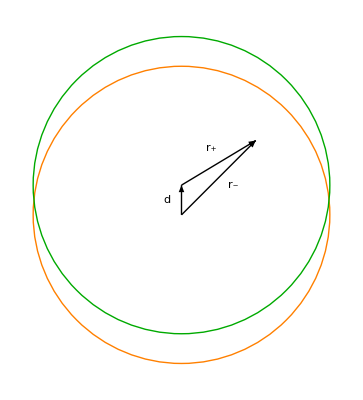

```mathematica
Graphics[{Style[Text["r_+",{.2,.45}],16,Bold],Style[Text["r_-",{.35,.2}],16,Bold],Style[Text["d",{-.1,.1}],16,Bold],Arrow[{{0,0},{0,.2}}],Arrow[{{0,0},{.5,.5}}],Arrow[{{0,.2},{.5,.5}}],Orange,Circle[{0,0},1],Darker[Green],Circle[{0,.2},1]}]
```

3.5 Displacement Vector D

The total charge density may be written as the sum of bound and free charge densities.

ρ =ρ_f+ρ_b

The displacement vector is defined such that its divergence is equal to the free charge density.

("ε")_0∇\[Application]E =ρ =ρ_b+ρ_f= -∇\[Application]P +ρ_f

∇\[Application]( ("ε")_0E+P) =ρ_f

D≡ ("ε")_0E+P

∇\[Application]D =ρ_f

The looks like a good thing to do because we have gotten rid of both the bound charge and  ("ε")_0. Experimentally, however, we do not measure charge in the laboratory because it is too difficult. Instead we electric potential difference V which gives us the field E. There is no such equivalent potential for D, because D  is not guaranteed to have a vanishing curl.

∇× D=∇× P

One must be very careful when using D.  For, example, there is no valid Coulomb’s law for D. Historically, the displacement vector has caused problems even for Maxwell.

If we have a linear dielectric, the we may write D as

D= ("ε")_0E+P= ("ε")_0E+ ("ε")_0 χ_e E= ("ε")_0(1+χ_e)E=ε E

where

ε ≡  ("ε")_0(1+χ_e)

This is often written is terms of a relative permittivity (ε_r)

ε_r≡ε/ε_0=(1+χ_e)

It is seen then that the effect of a linear dielectric is to reduce the electric field by a factor of ε_r. For example, consider a point charge inside a dielectric. The displacement field may be found using Gauss’s law.

D=Q/(4π r^2)r̂

which gives
	E = D/ε=Q/(4π ε r^2)r̂

3.5.1 Line of Charge Inside an Insulator

The displacement vector is useful when symmetry allows the use of Gauss’s law. Consider a long line of charge (density λ) surrounded by a cylinder of insulating material of radius R.  Inside the insulator

D 2π r L= λ L

D = λ/(2π r) r̂

Draw the configuration for using Gauss’s law inside the dielectric.

```mathematica
Graphics3D[{Orange,Thickness[0.01],Line[{{-10,0,0},{10,0,0}}], Green,Opacity[.3],Cylinder[{{-1,0,0},{1,0,0}},3],Opacity[1],Black,Arrow[{{0,0,3},{0,0,5}}],Text["E",{0,0,5.4}],Opacity[.1],Cylinder[{{-10,0,0},{10,0,0}},5]},Boxed->False]
```

-Graphics3D-

Outside the insulator

D 2π r L= λ L

and the answer is exactly the same as inside. So everywhere,

D = λ/(2π  r) r̂

and it is noted that D is continuous at the boundary of the insulator.

Draw the configuration for using Gauss’s law outside the dielectric.

```mathematica
Graphics3D[{Orange,Thickness[0.01],Line[{{-10,0,0},{10,0,0}}], Green,Opacity[.3],Cylinder[{{-1,0,0},{1,0,0}},7],Opacity[1],Black,Arrow[{{0,0,7},{0,0,10}}],Text["E",{0,0,11}],Opacity[.1],Cylinder[{{-10,0,0},{10,0,0}},5]},Boxed->False]
```

-Graphics3D-

The field E is obtained from D using the expression

D= ("ε")_0E+P

Outside we have

E = λ/(2π  ("ε")_0 r) r̂

Inside, we cannot determine E without knowledge of P.

3.5.2 Uniform Field and Polarization with a Cavity

Suppose we have a region of material with a uniform field E_0 and uniform polarization P. This gives

D = ε_0 E_0 + P

What happens if we have a ball-shaped cavity inside the material?

```mathematica
Graphics3D[{Style[Text["P",{3,5,5}],18,Bold],Arrow[{{3.5,5,3},{3.5,5,7}}],Arrow[{{3.5,5,2},{6,3,4}}],Style[Text["E",{5,2.5,3}],18,Bold],{Darker[Green],Opacity[0.2],Cuboid[{0,0,0},{10,10,10}]},Opacity[1],Ball[{5,5,5},1]},Boxed->False]
```

-Graphics3D-

By superposition, the electric field inside the cavity is E_0 minus the field inside a uniformly polarized ball ball of material.

E_cavity = E_0 - E_ball

The portion of the field due to the ball has been previously calculated to be

E_ball=-P/(3 ε_0)

Therefore, inside the cavity

E_cavity = E_0 + P/(3 ε_0)

and

D_cavity = ε_0 E_0 + P/3

Suppose the cavity was the shape of a long cylinder (needle-like) parallel to P.

```mathematica
Graphics3D[{Style[Text["P",{3,5,5}],18,Bold],Arrow[{{3.5,5,3},{3.5,5,7}}],Arrow[{{3.5,5,2},{6,3,4}}],Style[Text["E",{5,2.5,3}],18,Bold],{Darker[Green],Opacity[0.2],Cuboid[{0,0,0},{10,10,10}]},Cylinder[{{5,5,3},{5,5,7}},.2]},Boxed->False]
```

-Graphics3D-

-Graphics3D-

The field due to a cylinder of polarization is that of 2 small charges on the ends separated by a large distance.

E_cylinder ≃ 0

The field in the cavity is

E_cavity = E_0 - E_cylinder≃E_0

D_cavity = ε_0 E_cavity≃ε_0 E_0

Now consider a cavity in the shape of a short cylinder (pancake-like) perpendicular to P.

```mathematica
Graphics3D[{Style[Text["P",{3,5,5}],18,Bold],Arrow[{{3.5,5,3},{3.5,5,7}}],Arrow[{{3.5,5,2},{6,3,4}}],Style[Text["E",{5,2.5,3}],18,Bold],{Darker[Green],Opacity[0.2],Cuboid[{0,0,0},{10,10,10}]},Cylinder[{{5,5,7.5},{5,5,8}},4]},Boxed->False]
```

-Graphics3D-

The electric field in the cavity is that of two sheets of bound charge ±σ_b.

E_cylinder ≃ -P/ε_0

E_cavity = E_0 - E_cylinder≃E_0+P/ε_0

D_cavity = ε_0 E_cavity≃ε_0 E_0+P

3.5.3 Boundary Conditions on  D

A discontinuity in perpendicular (normal) D occurs when there is a layer of free charge.

Draw a layer of free charge showing D.

```mathematica
Graphics3D[{Style[Text[Subscript["D", above],{6,6,3.5}],18,Bold],Arrow[{{5,5,.5},{5,5,3}}],Style[Text[Subscript["D", below],{6,6,-3.5}],18,Bold],Arrow[{{5,5,-.5},{5,5,-3}}],Table[Table[Style[Text["+",{i,j,0}],18,Darker[Red]],{i,0,10}],{j,0,10}],Style[Text["free charge",{11.5,11.5,0}],12,Darker[Red]]},Boxed->False]
```

-Graphics3D-

D_above - D_below=σ_f

A discontinuity in parallel D occurs when P has a non-zero curl.

```mathematica
Clear[D];Graphics3D[{Thickness[0.005],Style[Text[Subscript["D", below],{0,0,-1.4}],18,Bold],Arrow[{{.4,0,-1.2},{-.4,0,-1.2}}],Style[Text[Subscript["D", above],{0,0,-.6}],18,Bold],Arrow[{{-.4,0,-.8},{.4,0,-.8}}],Opacity[.3],Darker[Green],Cylinder[{{-1,0,0},{1,0,0}},1],Opacity[1],Style[Text["polarized material",{.5,0,1.3}],14],{Darker[Red],Style[Text["+",{1,0,0}],18,Bold]},Black,Style[Text["-",{-1,0,0}],18,Bold]},Boxed->False]
```

-Graphics3D-

The configuration above, a piece of material with permanent polarization, is called an electret. The field is that of a physical electric dipole. The electric field of an electret is analogous to the magnetic field of a permanent magnet. It is a collection of permanent electric dipoles just as a magnet is a collection of permanent magnetic dipoles.

3.5.3 Uniform Ball of Dielectric in External Field

Consider the example of a uniform ball of dielectric in a uniform external field. We shall work this problem 2 ways.

Method 1) Determining the polarization may be thought of as an iterative procedure with an applied electric field causing a polarization which in turn adds to the net field which changes the polarization. Assume the resulting polarization and electric field are linear inside the material and carry out the calculation, verifying the assumption.

Method 2) Solve Laplace’s equation

For method 1), assume that the contribution to the electric field from the resulting polarization inside is

E'_in

Then the net field causing the polarization is

E_in=E_0+E'_in

so we write

P=χ_e ε_0 E_in=(ε_r-1)ε_0 E_in

```mathematica
Graphics3D[{Style[Text[Subscript["E'", in],{.7,0,.25}],18,Bold],Arrow[{{.4,0,.5},{.4,0,0}}],Arrow[{{-.5,0,-.5},{-.5,0,.5}}],Style[Text["P",{-.2,0,0.}],18,Bold],Style[Text[Subscript["E", 0],{1.8,0,0.25}],18,Bold],Arrow[{{1.5,0,0},{1.5,0,.5}}],Orange, Opacity[0.2],Ball[]},Boxed->False]
```

-Graphics3D-

Now comes the assumption. If the field inside is uniform, then we know the relationship between E'_in and P because we worked that problem.

E'_in=-P/(3 ε_0)

This gives

E_in=E_0-P/(3 ε_0) =P/((ε_r-1)ε_0)

Solve for P

P=(3(ε_r-1))/(ε_r+2)ε_0 E_0

Check the solution

```mathematica
(1/(3 Subscript[ε, 0])+1/((Subscript[ε, r]-1)Subscript[ε, 0]))^-1 //Simplify
```

(3 ε_0 (-1+ε_r))/(2+ε_r)

We see that the polarization is indeed uniform which verifies that our assumption was correct.

E_in=P/((ε_r-1)ε_0)=1/((ε_r-1)ε_0)(3(ε_r-1))/(ε_r+2)ε_0 E_0=3/(ε_r+2)E_0

Our solution outside is that of a uniformly polarized sphere (which makes a perfect dipole) in an external field. The dipole strength is

p=(4π R^3)/3 P

where R is the radius of the ball.

E_out=E_0+p/(4π ε_0 r^3)(2 cosθ r̂+sinθ θ̂)

E_out=E_0 cosθ r̂-E_0 sinθ θ̂+(R^3 P)/(3 ε_0 r^3)(2 cosθ r̂+sinθ θ̂)

E_out=((2 R^3 P)/(3 ε_0 r^3)+E_0)cosθ r̂+((R^3 P)/(3 ε_0 r^3)-E_0)sinθ θ̂

For method 2), take the potential to be zero at the center of the sphere. Take the ẑ direction to be the direction of the external field. For the boundary condition at infinity, the ball does not contribute and we have to get our constant field.

V_out(r→∞)=-E_0z=-E_0r cosθ

such that

E_out=-∇V=-(∂V_out)/(∂z)ẑ=E_0 ẑ

The general solution outside may be written

V_out(r,θ)=-E_0r cosθ+∑_(l=0)^∞ B_l/r^(l+1)P_l(cosθ)

V_in(r,θ)=∑_(l=0)^∞ A_l r^l P_l(cosθ)

The boundary conditions are that the potential is continuous at the boundary of the sphere (r = R) and that the perpendicular component of the electric field must change by an amount σ/ε_0 where σ is the total surface charge density at the boundary which in the present problem is all bound charge. The first boundary condition immediately tells us that the solution can contain only

P_1(cosθ)=cosθ

and that

A_1 R P_1=-E_0R P_1+B_1/r^2 P_1

or

A_1=-E_0+B_1/R^3

The BC on the electric field gives

[(- (∂V_out)/(∂r))-(-(∂V_in)/(∂r))]_(r = R)=σ/ε_0=Pcosθ/ε_0=-(χ_e ε_0 A_1 cosθ)/ε_0

where we have used

P=χ_e ε_0 E_in=-χ_e ε_0 A_1 ẑ

Therefore

E_0+(2 B_1)/R^3+A_1=-χ_e A_1

or

E_0+(2 B_1)/R^3=-(χ_e+1)A_1

Multiply by ε_0

ε_0(E_0+(2 B_1)/R^3)=-ε_0(χ_e+1)A_1=-εA_1

This is just the BC on D. The normal component of D changes only when there is a free charge at the boundary. Since there is no free charge,

D=ε E

is continuous.

ε E_in=ε_0 E_out

-ε (∂V_in)/(∂r)=-ε_0(∂V_out)/(∂r)

The two equations to solve are

A_1=-E_0+B_1/r^3		(E_0+(2 B_1)/R^3)=-ε_r A_1

where ε_r=ε/ε_0 .

```mathematica
Solve[Subscript[A, 1]==-Subscript[Ε, 0]+Subscript[B, 1]/R^3 && Subscript[Ε, 0]+(2 Subscript[B, 1])/R^3==-Subscript[ε, r] Subscript[A, 1],{Subscript[A, 1],Subscript[B, 1]}]
```

{{A_1→-(3 Ε_0)/(2+ε_r),B_1→-(R^3 Ε_0-R^3 ε_r Ε_0)/(2+ε_r)}}

This is the same result that we had before, constant inside

E_in=-A_1=3/(2+ε_r)Ε_0

and constant plus a dipole outside

E_out=Ε_0+(2 B_1 cosθ)/r^3 r̂+B_1/r^3 sinθ θ̂=Ε_0-((R^3 Ε_0-R^3 ε_r Ε_0)/(2+ε_r))((2cosθ)/r^3 r̂+sinθ/r^3 θ̂)

E_out==Ε_0+ Ε_0 R^3((ε_r -1)/(2+ε_r))((2cosθ)/r^3 r̂+sinθ/r^3 θ̂)

This is the same as we had before which was

P=(3(ε_r-1))/(ε_r+2)ε_0 E_0

p=(4π R^3)/3 P

and

E_out=E_0+p/(4π ε_0 r^3)(2 cosθ r̂+sinθ θ̂)

3.6 Capacitance

A capacitor is formed by 2 conductors with charge ±Q having a potential difference of ∆V  and is defined to be

C≡Q/(∆V)

The unit of capacitance is C/V for which we give the special designation farad (F). Notice that when evaluating C, it does not depend on Q or ΔV  because ΔV  is proportional to Q. The capacitance is strictly a geometric factor.

Capacitance can alo be calculated for a single conductor with respect to another at infinity.

Calculate the capacitance of the earth.

```mathematica
R=Entity["Planet","Earth"][EntityProperty["Planet","Radius"]];   N[UnitConvert[4 π Quantity[, "ElectricConstant"] R,Quantity[, "Farads"]],1]
```

0.0007 F

It is seen that the farad is an enormous capacitance. Capacitance is typically measured in pF corresponding to cm distance scales.

Calculate the capacitance of a 1 cm radius conducting sphere.

```mathematica
R= 1 Quantity[, "Centimeters"];  N[ UnitConvert[4 π Quantity[, "ElectricConstant"] R, Quantity[, "Picofarads"]],3]
```

1.11 pF

3.6.1 Parallel-Plate Capacitor

The most common capacitor is that formed with parallel plates of area A separated by distance d. The plates can be any shape but usually are taken to be either disks or squares. The fringe fields are neglected.

Draw a parallel-plate capacitor.

```mathematica
Graphics3D[{Style[Text["-",{0,0,-1.001}],18],{Darker[Red],Style[Text["+",{0,0,1}],18]},Gray,Opacity[0.1],Cylinder[{{0,0,-1},{0,0,-1.001}},5],Cylinder[{{0,0,1},{0,0,1.001}},5]},Boxed->False]
```

-Graphics3D-

If they have charges ±Q then the electric field is

E = σ/(("ε")_0)=Q/(A  ("ε")_0)

the potential difference between the plates is

ΔV=E d =(Q d)/(A  ("ε")_0)

and the capacitance is

C=Q/ΔV=(A  ("ε")_0)/d

Calculate the capacitance for A=1  ("cm")^2 and  d=1 "mm".

```mathematica
A=1 Quantity[, ("Centimeters")^2];  d=1 Quantity[, "Millimeters"];  N[UnitConvert[ (A Quantity[, "ElectricConstant"])/d, Quantity[, "Picofarads"]],2]
```

0.89 pF

3.6.2 Capacitor with Dielectric

If the space between the plates is filled with dielectric material, the the field is reduced by ε_r.

Draw a parallel-plate capacitor with material between the plates.

```mathematica
Graphics3D[{Style[Text["-",{0,0,-1.001}],18],{Darker[Red],Style[Text["+",{0,0,1}],18]},Gray,Opacity[0.1],Cylinder[{{0,0,-1},{0,0,-1.001}},5],Cylinder[{{0,0,1},{0,0,1.001}},5],Darker[Green],Cylinder[{{0,0,-1},{0,0,1}},5]},Boxed->False]
```

-Graphics3D-

E=Q/(A ε)

and the capacitance increases by ε_r.

C=(A ε)/d

Calculate the capacitance for A=1  ("cm")^2 and  d=1 "mm" filled with polyimide.

```mathematica
A=1 Quantity[, ("Centimeters")^2];  d=1 Quantity[, "Millimeters"];  NumberForm[UnitConvert[ (A Quantity[, "ElectricConstant"])/d 3.6, Quantity[, "Picofarads"]],3]
```

3.19 pF

The dielectric constant of polyimide is obtained with Ctrl+ permittivity polyimide, LinguisticAssistant

3.7 Point Charge Near a Dielectric Boundary

Consider a point charge at a distance d from the plane of a dielectric boundary which is semi-infinite in extent.

```mathematica
Clear[q];Graphics3D[{Line[{{0,0,2},{0,0,6}}],Style[Text["d",{-1,0,4}],18],Line[{{0,0,2},{0,4,2}}],Style[Text["r",{0,2,1.6}],18],Opacity[0.1],Darker[Green],Cylinder[{{0,0,0},{0,0,2}},8],Opacity[1],Orange,PointSize[0.02],Point[{0,0,6}],Style[Text[q,{1.5,0,6}],18],},Boxed->False]
```

-Graphics3D-

The surface bound charge density is

σ_b= P \[Application] n̂= ("ε")_0 χ_e E_(z,below)

where E_(z,below) is the field just below the surface inside the dielectric. The boundary condition says that E_z is discontinuous by the amount of surface charge density. The quantity E_(z,below) is the sum of two contributions, that of the bound surface charge plus that of the point charge. Note that these two contributions point in opposite directions. This gives us an expression which can be used to solve for the bound charge density.

σ_b= ("ε")_0 χ_e [-σ_b/(2 ε_0)-(q d)/(4π ε_0 (r^2+d^2)^(3/2))]

This gives

σ_b= -1/(2π)(χ_e/(χ_e+2))(q d)/((r^2+d^2)^(3/2))

This is the same as a point charge near a conducting plane, except for the dielectric factor. This example can also be worked by the method of images.

Find the bound charge density for q =  1  "μ" "C" at distance  d=1  "cm" for r =10   "cm".

```mathematica
εr=2; χ=εr-1;q= 1 Quantity[, "Micro"]Quantity[, "Coulombs"]; d=1 Quantity[, "Centimeters"]; r =10  Quantity[, "Centimeters"];σ=N[-1/(2 π)χ/(χ+2)(q d)/((r^2+d^2)^(3/2)),2]
```

-0.000052 μ C/cm^2

Find the number of electrons per square m.

```mathematica
UnitConvert[-σ/Quantity[, "ElementaryCharge"]]
```

3.3×10^12 per meter^2

3.8 Stored Energy in Dielectrics

The energy stored in a charged capacitor is

W=1/2 C(ΔV)^2

The assembly of all charges, free and bound, may be written as the pure total electrostatic energy

W=(("ε")_0)/2∫ E^2 ⅆ𝕍

If instead, one is only counting the assembly of free charges and the stretching of the charges in a dielectric, the energy is

W=(("ε")_0)/2∫ D\[Application]Eⅆ𝕍

Thus one needs to be careful about defining exactly what is meant by this energy. The same issue was encountered in the assembly of point charges where one needed to specify if the energy to make the point charge itself was included.

As an example, consider a ball of dielectric of radius R that is also filled with free electric charge that is uniformly distributed. For r <  R

D=ρ_f/3 r̂		 E=ρ_f/(3ε)r̂

and for  r > R

D=(ρ_f R^3)/(3 r^2)r̂		 E=(ρ_f R^3)/(3 ε_0 r^2)r̂

This gives

(("ε")_0)/2∫ E^2 ⅆ𝕍=(2 π ρ_f^2 R^5)/(9 ε_0)(ε_0^2/ε^2+1)

and

(("ε")_0)/2∫ D\[Application]Eⅆ𝕍=(2 π ρ_f^2 R^5)/(9 ε_0)(ε_0/ε+1)

Calculate the stored energy for R = 0.1 m , ρ_f = 1 mC/m, and ε_r= 2.

```mathematica
R=0.1 Quantity[, "Meters"]; ρ= 10^3 Quantity[, "Micro"]*Quantity[, ("Coulombs")/("Meters")^3]; εr=2;NumberForm[UnitConvert[(2π ρ^2 R^5)/(9 Quantity[, "ElectricConstant"])(εr+1),Quantity[, "Joules"]],3]
```

2.37 J

Exercises

Consider a point charge q that is a large distance r from a neutral atom that has polarizability α.
a) Explain why the atom and the charge will be attracted to one another.
b) Calculate the force of attraction.
c) Make an order of magnitude estimate of α/4πε_0 for the atom and use it to calculate a numerical value of the force between a proton and the atom at a distance of 100 nm. Compare your answer to the force between and electron and proton at the same distance.

Imagine bringing in charge from infinity and spreading it out on the surface of the earth. There will be a potential difference between the surface of the earth and infinity. Calculate the capacitance of the earth and give a numerical value in farads (F).

Consider a parallel capacitor with a combination of two dielectrics (ε_1 and ε_2). Find the capacitance for the cases a) the dielectrics are above and below each other such that their boundary is parallel to the plates and b) the dielectrics are side-by-side such that their boundary is perpendicular to the plates.

Consider a solid sphere of dielectric material of radius a that has a polarization vector P = C r, with C constant.
a) Find the bound charge density on the surface of the sphere.
b) Find the bound charge density inside the sphere.
c) Find the electric field vector outside the sphere.
d) Find the electric field vector inside the sphere.

Consider two concentric cylindrical conductors (a wire with a shield around it). The radius of the inside conductor (wire) is a and the inner radius of the outside shield is b.
a) Calculate the capacitance per unit length.
b) A plastic material is intrioduced in the space between the wire and the shield, making a coax cable. The RG59 coax cable consists of an inner wire of 0.29 mm, an outer shield of radius 1.86 mm and a dielectric factor of the plastic spacer of 2.25. Calculate the capacitance per length and give a numerical value in pF/m.

Work the example of a point charge near a dielectric boundary by the method of images.

Consider a conducting sphere of radius R surrounded by a shell of dielectric that extends to a distance d beyond the radius of the conductor. Calculate the stored energy by integrating D\[Application]E.

Consider a long cylinder in which P is constant and oriented perpendicular to the axis of the cylinder. Superimpose 2 cylinders of uniform charge density ±ρ analogous to what was done for the ball geometry. Let the separation distance between the axis of the cylinders be a tiny amount d.
a) Calculate the electric field inside the polarized cylinder.
b) Give an expression for the polarization vector.
c) Find the electric field outside the cylinder.
d) Show that the electric field outside can be written in terms of the constant polarization inside as
E ∼2 P \[Application] r r̂- P and find the constant of proportionality. Hint: Expand the exact expression for E and keep only leading powers of d.

Consider a uniform plane of free charge (density σ) That has linear dielectric material with permittivity ε_1 above the place and ε_2 below the plane.
a) Find the electric field everywhere.
b) Find the polarization vector everywhere.
c) Find the bound charge density at the interface of the two dielectrics.
d) Show that Gauss’s law is satisfied for a “pillbox” placed at the interface.

Consider a uniformly polarized sphere of permanent polarization P.
a) Is this a linear dielectric? Explain.
b) Calculate the pure electrostatic energy of this configuration.
c) Calculate the stored energy by integrating D\[Application]E.
d) Give some physical interpretation for the answers obtained in b) and c).

Verify your understanding of the force on a single dipole in a non-uniform external field to be
F = (p⋄∇) E_ext. Now generalized this to a dielectric with polarization,  F = ∫ (P⋄∇) E_ext ⅆ𝕍. Calculate this force for a small ball of linear dielectric (χ_e) at a distance r from a long uniform line of charge with charge per length λ. You may assume that the ball is small enough so that the polarization is constant.

Consider a point charge at the center of a dielectric ball of radius a characterized by ε and χ_e.
a) Determine D everywhere and then get E from D  and use the boundary condition on E at the surface of the dielectric ball to get the bound charge density.
b) Calculate the polarization and use it to get the bound charge on the surface of the dielectric sphere arriving at the same answer as a).
c) Calculate the volume bound charge density.
d) Calculate the electric field directly from q, ρ_b, and σ_band show that you get the same result as in a).